```mathematica
(* Subscript[I, 2](l,L) at 2 T_c with free b.c.
=c/2 ln[(f(l/L) f((L-l)/L))/(√L f(1))]
where f(x)=Dedekindeta(ix) *)
```

```mathematica
(* Subscript[I, 2](l,L)-Subscript[I, 2](L/2,L) *)
Log[F[x,L]]-Log[F[1/2,L]]//FullSimplify
```

Log[L]/2+Log[(DedekindEta[-ⅈ (-1+x)] DedekindEta[ⅈ x])/(√L DedekindEta[ⅈ/2]^2)]

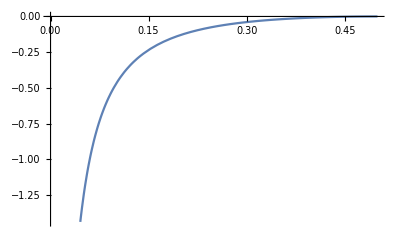

```mathematica
Clear[J,l,L,x,F,c];
(* for classical Blume-Capel model *)
c=7/10;
F[x_]:=(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2;
p=Plot[c/2 Log[F[x]],{x,0,0.5}]
```

```mathematica
(* fit data *)
```

{{0.03125,-1.1514},{0.033333,-1.0618},{0.035714,-0.97113},{0.038462,-0.87422},{0.041667,-0.78188},{0.045455,-0.68508},{0.05,-0.59441},{0.055556,-0.50321},{0.0625,-0.71376},{0.0625,-0.41311},{0.066667,-0.65437},{0.071429,-0.59571},{0.071429,-0.32993},{0.076923,-0.52907},{0.083333,-0.24826},{0.083333,-0.4675},{0.090909,-0.4018},{0.09375,-0.46985},{0.1,-0.42518},{0.1,-0.34149},{0.1,-0.17336},{0.10714,-0.38525},{0.11111,-0.2813},{0.11538,-0.33677},{0.125,-0.10874},{0.125,-0.29286},{0.125,-0.31577},{0.125,-0.22197},{0.13333,-0.28372},{0.13636,-0.24782},{0.14286,-0.25383},{0.14286,-0.16895},{0.15,-0.20536},{0.15385,-0.21813},{0.15625,-0.21361},{0.16667,-0.18955},{0.16667,-0.11705},{0.16667,-0.16396},{0.16667,-0.18689},{0.16667,-0.056205},{0.17857,-0.16994},{0.18182,-0.15401},{0.1875,-0.14812},{0.1875,-0.12263},{0.19231,-0.1427},{0.2,-0.12909},{0.2,-0.12363},{0.2,-0.072026},{0.20833,-0.11864},{0.21429,-0.11341},{0.21429,-0.087571},{0.21875,-0.10134},{0.22222,-0.0944},{0.22727,-0.09582},{0.23077,-0.093125},{0.23333,-0.087232},{0.25,-0.054306},{0.25,-0.035907},{0.25,-0.073389},{0.25,-0.075255},{0.25,-0.076006},{0.25,-0.069798},{0.25,-0.065467},{0.26667,-0.059664},{0.26923,-0.060767},{0.27273,-0.057884},{0.27778,-0.05232},{0.28125,-0.046634},{0.28571,-0.049876},{0.28571,-0.042523},{0.29167,-0.046519},{0.3,-0.039021},{0.3,-0.041469},{0.3,-0.026917},{0.30769,-0.037889},{0.3125,-0.031756},{0.3125,-0.031025},{0.31818,-0.033888},{0.32143,-0.032009},{0.33333,-0.023648},{0.33333,-0.020984},{0.33333,-0.026997},{0.33333,-0.026502},{0.33333,-0.010501},{0.34375,-0.020992},{0.34615,-0.021303},{0.35,-0.020717},{0.35714,-0.018409},{0.35714,-0.017319},{0.36364,-0.018515},{0.36667,-0.013433},{0.375,-0.0080236},{0.375,-0.014052},{0.375,-0.012888},{0.375,-0.011606},{0.38462,-0.011283},{0.38889,-0.01152},{0.39286,-0.0091603},{0.4,-0.0062821},{0.4,-0.0083981},{0.4,-0.0059728},{0.40625,-0.0083756},{0.40909,-0.0080276},{0.41667,-0.0047017},{0.41667,-0.0060344},{0.42308,-0.0050479},{0.42857,-0.0038068},{0.42857,-0.0041341},{0.43333,-0.0018766},{0.4375,-0.0061236},{0.4375,-0.0026141},{0.44444,-0.0028674},{0.45,-0.001442},{0.45455,-0.0020297},{0.45833,-0.0015413},{0.46154,-0.001114},{0.46429,-0.00075072},{0.46667,-0.00008991},{0.46875,-0.0024208}}

{c→0.379516}

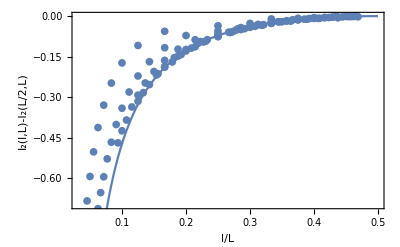

```mathematica
SetDirectory[NotebookDirectory[]];
d=Import["tot.dat"];
a=d[[;;,2]];
b=d[[;;,3]];
data=Transpose[{a,b}];
Sort[data,#1[[1]]<#2[[1]]&]
l=ListPlot[data];
fit=FindFit[data,J[c,x],{c},x]
(*******************)
Clear[J,x,F,c,pfit,pactual];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}];
Show[pactual,l,PlotRange->{-0.7,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"}]
(****************************************)
```

{c→0.653584}

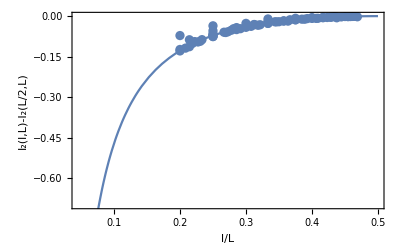

```mathematica
SetDirectory[NotebookDirectory[]];
datanew={{0.2,-0.12909},{0.2,-0.12363},{0.2,-0.072026},{0.20833,-0.11864},{0.21429,-0.11341},{0.21429,-0.087571},{0.21875,-0.10134},{0.22222,-0.0944},{0.22727,-0.09582},{0.23077,-0.093125},{0.23333,-0.087232},{0.25,-0.054306},{0.25,-0.035907},{0.25,-0.073389},{0.25,-0.075255},{0.25,-0.076006},{0.25,-0.069798},{0.25,-0.065467},{0.26667,-0.059664},{0.26923,-0.060767},{0.27273,-0.057884},{0.27778,-0.05232},{0.28125,-0.046634},{0.28571,-0.049876},{0.28571,-0.042523},{0.29167,-0.046519},{0.3,-0.039021},{0.3,-0.041469},{0.3,-0.026917},{0.30769,-0.037889},{0.3125,-0.031756},{0.3125,-0.031025},{0.31818,-0.033888},{0.32143,-0.032009},{0.33333,-0.023648},{0.33333,-0.020984},{0.33333,-0.026997},{0.33333,-0.026502},{0.33333,-0.010501},{0.34375,-0.020992},{0.34615,-0.021303},{0.35,-0.020717},{0.35714,-0.018409},{0.35714,-0.017319},{0.36364,-0.018515},{0.36667,-0.013433},{0.375,-0.0080236},{0.375,-0.014052},{0.375,-0.012888},{0.375,-0.011606},{0.38462,-0.011283},{0.38889,-0.01152},{0.39286,-0.0091603},{0.4,-0.0062821},{0.4,-0.0083981},{0.4,-0.0059728},{0.40625,-0.0083756},{0.40909,-0.0080276},{0.41667,-0.0047017},{0.41667,-0.0060344},{0.42308,-0.0050479},{0.42857,-0.0038068},{0.42857,-0.0041341},{0.43333,-0.0018766},{0.4375,-0.0061236},{0.4375,-0.0026141},{0.44444,-0.0028674},{0.45,-0.001442},{0.45455,-0.0020297},{0.45833,-0.0015413},{0.46154,-0.001114},{0.46429,-0.00075072},{0.46667,-0.00008991},{0.46875,-0.0024208}};
lnew=ListPlot[datanew];
fitnew=FindFit[datanew,J[c,x],{c},x]
(*******************)
Clear[J,x,F,c,pfit,pactual];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}];
Show[pactual,lnew,PlotRange->{-0.7,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"}]
(****************************************)
```

```mathematica
SetDirectory[NotebookDirectory[]];
(* for i in `ls MI*`;do cp $i newdir/$i.dat;done *)
(***************************************************)
b6=Import["MI2_L6_B0.64102.dat"];
a6={0/6,1/6,2/6,3/6,4/6,5/6,6/6};
bb6=b6[[;;,1]];
data6={{a6[[2]],bb6[[2]]},{a6[[3]],bb6[[3]]}};
(****************************************)
b8=Import["MI2_L8_B0.64102.dat"];
a8={0/8,1/8,2/8,3/8,4/8,5/8,6/8,7/8,8/8};
bb8=b8[[;;,1]];
data8={{a8[[2]],bb8[[2]]},{a8[[3]],bb8[[3]]},{a8[[4]],bb8[[4]]}};
(*************************************)
b10=Import["MI2_L10_B0.64102.dat"];
Clear[p];
p=10;
a10={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p};
bb10=b10[[;;,1]];
data10={{a10[[2]],bb10[[2]]},{a10[[3]],bb10[[3]]},{a10[[4]],bb10[[4]]},{a10[[5]],bb10[[5]]}};
(*************************************)
b12=Import["MI2_L12_B0.64102.dat"];
Clear[p];
p=12;
a12={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p};
bb12=b12[[;;,1]];
data12={{a12[[2]],bb12[[2]]},{a12[[3]],bb12[[3]]},{a12[[4]],bb12[[4]]},{a12[[5]],bb12[[5]]},{a12[[6]],bb12[[6]]}};
(*************************************)
b14=Import["MI2_L14_B0.64102.dat"];
Clear[p];
p=14;
a14={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p};
bb14=b14[[;;,1]];
data14={{a14[[2]],bb14[[2]]},{a14[[3]],bb14[[3]]},{a14[[4]],bb14[[4]]},{a14[[5]],bb14[[5]]},{a14[[6]],bb14[[6]]},{a14[[7]],bb14[[7]]}};
(*************************************)
b16=Import["MI2_L16_B0.64102.dat"];
Clear[p];
p=16;
a16={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p};
bb16=b16[[;;,1]];
data16={{a16[[2]],bb16[[2]]},{a16[[3]],bb16[[3]]},{a16[[4]],bb16[[4]]},{a16[[5]],bb16[[5]]},{a16[[6]],bb16[[6]]},{a16[[7]],bb16[[7]]},{a16[[8]],bb16[[8]]}};
(*************************************)
b18=Import["MI2_L18_B0.64102.dat"];
Clear[p];
p=18;
a18={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p};
bb18=b18[[;;,1]];
data18={{a18[[2]],bb18[[2]]},{a18[[3]],bb18[[3]]},{a18[[4]],bb18[[4]]},{a18[[5]],bb18[[5]]},{a18[[6]],bb18[[6]]},{a18[[7]],bb18[[7]]},{a18[[8]],bb18[[8]]},{a18[[9]],bb18[[9]]}};
(*************************************)
b20=Import["MI2_L20_B0.64102.dat"];
Clear[p];
p=20;
a20={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p,19/p,20/p};
bb20=b20[[;;,1]];
data20={{a20[[2]],bb20[[2]]},{a20[[3]],bb20[[3]]},{a20[[4]],bb20[[4]]},{a20[[5]],bb20[[5]]},{a20[[6]],bb20[[6]]},{a20[[7]],bb20[[7]]},{a20[[8]],bb20[[8]]},{a20[[9]],bb20[[9]]},{a20[[10]],bb20[[10]]}};
(*************************************)
b22=Import["MI2_L22_B0.64102.dat"];
Clear[p];
p=22;
a22={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p,19/p,20/p,21/p,22/p};
bb22=b22[[;;,1]];
data22={{a22[[2]],bb22[[2]]},{a22[[3]],bb22[[3]]},{a22[[4]],bb22[[4]]},{a22[[5]],bb22[[5]]},{a22[[6]],bb22[[6]]},{a22[[7]],bb22[[7]]},{a22[[8]],bb22[[8]]},{a22[[9]],bb22[[9]]},{a22[[10]],bb22[[10]]}};
(*************************************)
b24=Import["MI2_L24_B0.64102.dat"];
Clear[p];
p=24;
a24={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p,19/p,20/p,21/p,22/p,23/p,24/p};
bb24=b24[[;;,1]];
data24={{a24[[2]],bb24[[2]]},{a24[[3]],bb24[[3]]},{a24[[4]],bb24[[4]]},{a24[[5]],bb24[[5]]},{a24[[6]],bb24[[6]]},{a24[[7]],bb24[[7]]},{a24[[8]],bb24[[8]]},{a24[[9]],bb24[[9]]},{a24[[10]],bb24[[10]]},{a24[[11]],bb24[[11]]},{a24[[12]],bb24[[12]]}};
(*****************************************)
b30=Import["MI2_L30_B0.64102.dat"];
Clear[p];
p=30;
a30={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p,19/p,20/p,21/p,22/p,23/p,24/p,25/p,26/p,27/p,28/p,29/p,30/p};
bb30=b30[[;;,1]];
data30={{a30[[2]],bb30[[2]]},{a30[[3]],bb30[[3]]},{a30[[4]],bb30[[4]]},{a30[[5]],bb30[[5]]},{a30[[6]],bb30[[6]]},{a30[[7]],bb30[[7]]},{a30[[8]],bb30[[8]]},{a30[[9]],bb30[[9]]},{a30[[10]],bb30[[10]]},{a30[[11]],bb30[[11]]},{a30[[12]],bb30[[12]]},{a30[[13]],bb30[[13]]},{a30[[14]],bb30[[14]]},{a30[[15]],bb30[[15]]}};

(*****************************************)
b32=Import["MI2_L32_B0.64102.dat"];
Clear[p];
p=32;
a32={0/p,1/p,2/p,3/p,4/p,5/p,6/p,7/p,8/p,9/p,10/p,11/p,12/p,13/p,14/p,15/p,16/p,17/p,18/p,19/p,20/p,21/p,22/p,23/p,24/p,25/p,26/p,27/p,28/p,29/p,30/p,31/p,32/p};
bb32=b32[[;;,1]];
data32={{a32[[2]],bb32[[2]]},{a32[[3]],bb32[[3]]},{a32[[4]],bb32[[4]]},{a32[[5]],bb32[[5]]},{a32[[6]],bb32[[6]]},{a32[[7]],bb32[[7]]},{a32[[8]],bb32[[8]]},{a32[[9]],bb32[[9]]},{a32[[10]],bb32[[10]]},{a32[[11]],bb32[[11]]},{a32[[12]],bb32[[12]]},{a32[[13]],bb32[[13]]},{a32[[14]],bb32[[14]]},{a32[[15]],bb32[[15]]},{a32[[16]],bb32[[16]]}};
(*************************************)
```

{c→0.207952}

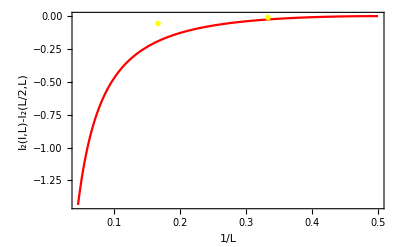

{c→0.238575}

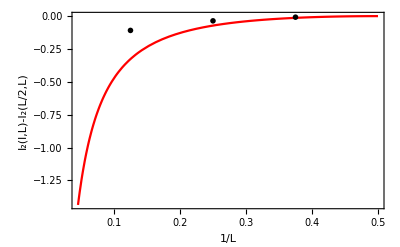

{c→0.267285}

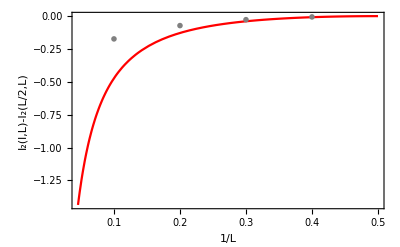

{c→0.293867}

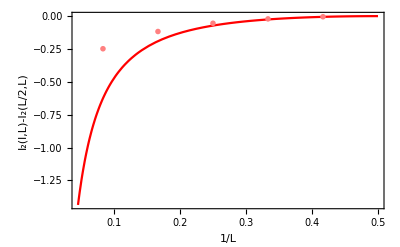

{c→0.316466}

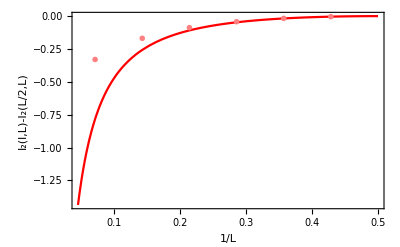

{c→0.331921}

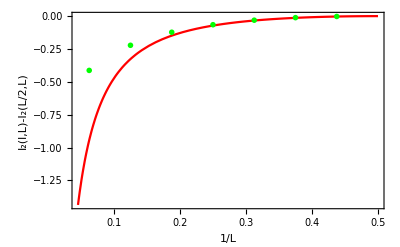

{c→0.348172}

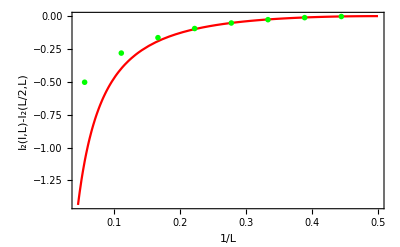

{c→0.360415}

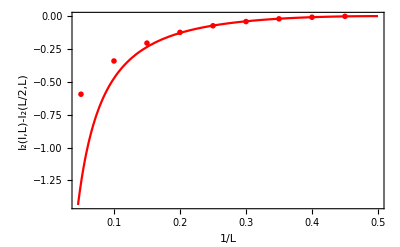

{c→0.369455}

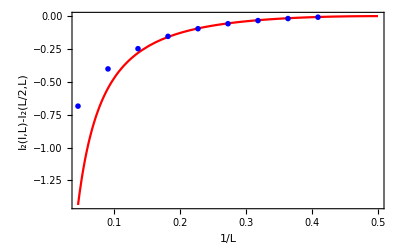

{c→0.37955}

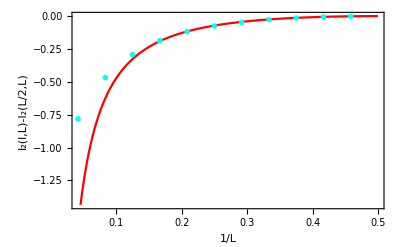

{c→0.396963}

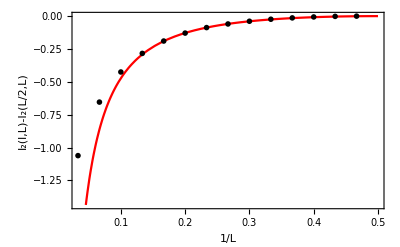

{c→0.396963}

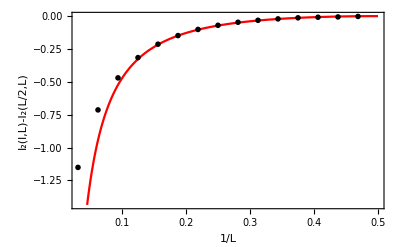

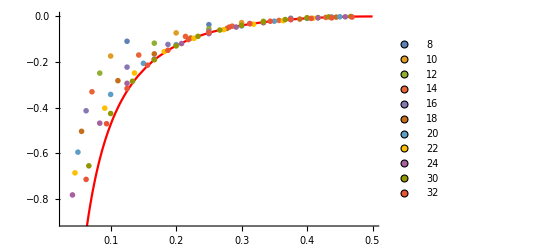

```mathematica
(* without (l=1)/L data point*)
(*SetDirectory[NotebookDirectory[]];*)
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ/2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Red}];
(***************)
marker1=Graphics[{Disk[]}];
l6=ListPlot[data6,PlotStyle->Yellow,PlotMarkers->{marker1,.03}];
fit6=FindFit[data6,J[c,x],{c},x]
Show[pactual,l6,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=6"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l8=ListPlot[data8,PlotStyle->Black,PlotMarkers->{marker1,.03}];
fit8=FindFit[data8,J[c,x],{c},x]
Show[pactual,l8,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=8"}}]
(*aaaaaaaaaaaaaaaaaaaaa*)
l10=ListPlot[data10,PlotStyle->Gray,PlotMarkers->{marker1,.03}];
fit10=FindFit[data10,J[c,x],{c},x]
Show[pactual,l10,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=10"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l12=ListPlot[data12,PlotStyle->Pink,PlotMarkers->{marker1,.03}];
fit12=FindFit[data12,J[c,x],{c},x]
Show[pactual,l12,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=12"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l14=ListPlot[data14,PlotStyle->Pink,PlotMarkers->{marker1,.03}];
fit14=FindFit[data14,J[c,x],{c},x]
Show[pactual,l14,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=14"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l16=ListPlot[data16,PlotStyle->Green,PlotMarkers->{marker1,.03}];
fit16=FindFit[data16,J[c,x],{c},x]
Show[pactual,l16,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=16"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l18=ListPlot[data18,PlotStyle->Green,PlotMarkers->{marker1,.03}];
fit18=FindFit[data18,J[c,x],{c},x]
Show[pactual,l18,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=18"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
l20=ListPlot[data20,PlotStyle->Red,PlotMarkers->{marker1,.03}];
fit20=FindFit[data20,J[c,x],{c},x]
Show[pactual,l20,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=20"}}]
(***************)
l22=ListPlot[data22,PlotStyle->Blue,PlotMarkers->{marker1,.03}];
fit22=FindFit[data22,J[c,x],{c},x]
Show[pactual,l22,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=22"}}]
(*aaaaaaaaaaaaaaaaaaaaaaaaaaaaa*)
SetDirectory[NotebookDirectory[]];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ/2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Red}];
(***************)
l24=ListPlot[data24,PlotStyle->Cyan,PlotMarkers->{marker1,.03}];
fit24=FindFit[data24,J[c,x],{c},x]
Show[pactual,l24,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=24"}}]
(***************)
l30=ListPlot[data30,PlotStyle->Black,PlotMarkers->{marker1,.03}];
fit30=FindFit[data32,J[c,x],{c},x]
Show[pactual,l30,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=30"}}]
(***************)
l32=ListPlot[data32,PlotStyle->Black,PlotMarkers->{marker1,.03}];
fit32=FindFit[data32,J[c,x],{c},x]
Show[pactual,l32,PlotRange->Automatic,Frame->True,FrameLabel->{{"I_2(l,L)-I_2(L/2,L)",None},{"1/L","L=32"}}]
(*********************)
LLL=ListPlot[{data8,data10,data12,data14,data16,data18,data20,data22,data24,data30,data32},PlotLegends->{8,10,12,14,16,18,20,22,24,30,32},PlotMarkers->{marker1,.03}];
s=Show[pactual,LLL,PlotRange->{-0.9,0}]
(*Export["all-data-ips.pdf",s];
Show[pactual,l8,l10,l12,l14,l12,l16,l18,l20,l24,PlotRange->{-0.2,0}]*)
```

```mathematica
(* c extrapolation to L->∞*)
```

```mathematica
(* l/L=1/6 *)
dat1={{1/6,bb6[[2]]},{1/12,bb12[[3]]},{1/18,bb18[[4]]},{1/24,bb24[[5]]}}
```

{{1/6,-0.0562053},{1/12,-0.117045},{1/18,-0.163962},{1/24,-0.186888}}

```mathematica
(* l/L=1/6 *)
Clear[lbL,f,m,i,dat];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL1=1.0/6;
J[0.7,lbL1]
line1=Fit[dat1,{1,x},x](* x = 1/L *)
f=FindFit[dat1,m x +i,{m,i},x];
v1=i/.f[[2]];
```

-0.190536

-0.21851+1.00782 x

```mathematica
(* l/L=1/3 *)
dat2={{1/6,bb6[[3]]},{1/12,bb12[[5]]},{1/18,bb18[[7]]},{1/24,bb24[[9]]}}
```

{{1/6,-0.0105008},{1/12,-0.0209844},{1/18,-0.026997},{1/24,-0.026502}}

```mathematica
(* l/L=1/3 *)
Clear[lbL,f,m,i,dat];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL2=1.0/3;
J[0.7,lbL2]
line2=Fit[dat2,{1,x},x](* x = 1/L *)
f=FindFit[dat2,m x +i,{m,i},x];
v2=i/.f[[2]];
```

-0.0252287

-0.0330077+0.135495 x

```mathematica
(* l/L=1/4 *)
dat3={{1/8,bb8[[3]]},{1/16,bb16[[5]]},{1/24,bb24[[7]]}}
```

{{1/8,-0.0359068},{1/16,-0.0654667},{1/24,-0.0752548}}

```mathematica
(* l/L=1/4 *)
Clear[lbL,f,m,i,dat];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL3=1.0/4;
J[0.7,lbL3]
f=FindFit[dat3,m x +i,{m,i},x];
v3=i/.f[[2]];
line3=Fit[dat3,{1,x},x](* x = 1/L *)
```

-0.0719068

-0.0949588+0.472356 x

```mathematica
(* l/L=1/5 *)
dat4={{1/10,bb10[[3]]},{1/20,bb20[[5]]},{1/30,bb30[[7]]}}
```

{{1/10,-0.0720259},{1/20,-0.12363},{1/30,-0.129087}}

```mathematica
(* l/L=1/5 *)
Clear[lbL,f,m,i,dat];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL4=1.0/5;
J[0.7,lbL4]
f=FindFit[dat4,m x +i,{m,i},x];
v4=i/.f[[2]];
line4=Fit[dat4,{1,x},x](* x = 1/L *)
```

-0.1282

-0.163039+0.896577 x

```mathematica
(* l/L=2/5 *)
dat5={{1/10,bb10[[5]]},{1/20,bb20[[9]]},{1/30,bb30[[13]]}}
```

{{1/10,-0.00597281},{1/20,-0.00839806},{1/30,-0.00628211}}

```mathematica
(* l/L=2/5 *)
Clear[lbL,f,m,i,dat];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL5=2.0/5;
J[0.7,lbL5]
f=FindFit[dat5,m x +i,{m,i},x];
v5=i/.f[[2]];
line5=Fit[dat5,{1,x},x](* x = 1/L *)
```

-0.00813531

-0.00500212-0.0095992 x

```mathematica
(* l/L=1/8 *)
dat6={{1/8,bb8[[2]]},{1/16,bb16[[3]]},{1/24,bb24[[4]]}}
```

{{1/8,-0.108742},{1/16,-0.221975},{1/24,-0.292863}}

```mathematica
(* l/L=1/8 *)
Clear[lbL,f,m,i,dat];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL6=1.0/8;
J[0.7,lbL6]
f=FindFit[dat6,m x +i,{m,i},x];
v6=i/.f[[2]];
line6=Fit[dat6,{1,x},x](* x = 1/L *)
```

0.35 Log[(DedekindEta[ⅈ (1-lbL)] DedekindEta[ⅈ lbL])/DedekindEta[ⅈ/2]^2]

-0.369626+2.11767 x

```mathematica
(* l/L=1/10 *)
dat7={{1/10,bb10[[2]]},{1/20,bb20[[3]]},{1/30,bb30[[4]]}}
```

```mathematica
{{1/10,-0.17336479},{1/20,-0.34148654},{1/30,-0.42518273}}
```

{{1/10,-0.173365},{1/20,-0.341487},{1/30,-0.425183}}

```mathematica
(* l/L=1/10 *)
Clear[lbL,i,m,dat,f];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL7=1.0/10;
J[0.7,lbL7]
f=FindFit[dat7,m x +i,{m,i},x];
v7=i/.f[[2]];
line7=Fit[dat7,{1,x},x](* x = 1/L *)
```

-0.473124

-0.538328+3.68154 x

```mathematica
(* l/L=3/10 *)
dat8={{1/10,bb10[[4]]},{1/20,bb20[[7]]},{1/30,bb30[[10]]}}
```

{{1/10,-0.026917},{1/20,-0.0414687},{1/30,-0.0390205}}

```mathematica
(* l/L=3/10 *)
Clear[m,i,f];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL8=3.0/10;
J[0.7,lbL8]
f=FindFit[dat8,m x +i,{m,i},x];
v8=i/.f[[2]];
line8=Fit[dat8,{1,x},x](* x = 1/L *)
```

-0.0393431

-0.048441+0.206818 x

```mathematica
(* l/L=3/8 *)
dat9={{1/8,bb8[[4]]},{1/16,bb16[[7]]},{1/24,bb24[[10]]}}
```

{{1/8,-0.00802358},{1/16,-0.011606},{1/24,-0.0140521}}

```mathematica
(* l/L=3/8 *)
Clear[m,i,f];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL9=3.0/8;
J[0.7,lbL9]
f=FindFit[dat9,m x +i,{m,i},x];
v9=i/.f[[2]];
line9=Fit[dat9,{1,x},x](* x = 1/L *)
```

-0.013153

-0.0164885+0.0688752 x

```mathematica
(* l/L=1/12 *)
dat10={{1/12,bb12[[2]]},{1/24,bb24[[3]]}}
```

{{1/12,-0.248259},{1/24,-0.467504}}

```mathematica
Clear[m,i,f];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL10=1.0/12;
J[0.7,lbL10]
f=FindFit[dat10,m x +i,{m,i},x];
v10=i/.f[[2]];
line10=Fit[dat10,{1,x},x](* x = 1/L *)
```

-0.625881

-0.68675+5.26189 x

```mathematica
(* l/L=5/12 *)
dat11={{1/12,bb12[[6]]},{1/24,bb24[[11]]}}
```

{{1/12,-0.00470166},{1/24,-0.00603443}}

```mathematica
(* l/L=5/12 *)
Clear[f,i,m];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
lbL11=5.0/12;
J[0.7,lbL11]
f=FindFit[dat11,m x +i,{m,i},x];
v11=i/.f[[2]];
line11=Fit[dat11,{1,x},x](* x = 1/L *)
```

-0.00554708

-0.0073672+0.0319865 x

{c→0.784927}

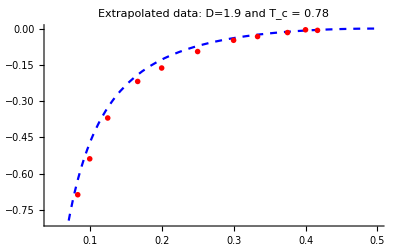

```mathematica
Clear[J,pactual,c];
J[c_,lbL_]:=c/2 Log[(DedekindEta[ⅈ lbL]*DedekindEta[ⅈ (1-lbL)])/DedekindEta[ⅈ/2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5}, PlotStyle->{Dashed, Blue}];
dataextr={{lbL1,v1},{lbL2,v2},{lbL3,v3},{ lbL4 ,v4},{lbL5,v5},{lbL6,v6},{lbL7,v7},{lbL8,v8},{lbL9,v9},{lbL10,v10},{lbL11,v11}};
FindFit[dataextr,J[c,x],{c},x]
plotextr=ListPlot[dataextr,PlotStyle->Red,PlotMarkers->{marker1,.03}];
Show[{pactual,plotextr},PlotRange->{-0.8,0},PlotLabel->"Extrapolated data: D=1.9 and T_c = 0.78"]
```